```mathematica
root="/Users/dfremont/Documents/Programming/rci/experiments/loop/";
ids=Range[0,3];
mt=Map[Import[root<>"traj"<>ToString[#]<>".csv"]&,ids];
at=Map[Import[root<>"traj"<>ToString[#]<>"a.csv"]&,ids];
fmt=Map[Map[{#[[2]],#[[3]]}&,#]&,mt];
fat=Map[Map[{#[[2]],#[[3]]}&,#]&,at];
```

```mathematica
r=1;
locs={Red,Disk[gp[{2,2}],r],Disk[gp[{4,2}],r],Disk[gp[{2,4}],r],Disk[gp[{4,4}],r],Gray,RegularPolygon[gp[{3,3}],2r,4],Green,RegularPolygon[gp[{0,0}],1.5r,3],RegularPolygon[gp[{5,5}],1.5r,3]};
```

```mathematica
lmt=fmt;
lat=fat;
llocs=locs;
```

```mathematica
cmt=fmt;
cat=fat;
clocs=locs;
```

```mathematica
gp[x_]:=(x-3)*(10/3);
SetAttributes[gp,Listable];
```

```mathematica
mpts=100;
pr=12.5;
plots=Table[ListLinePlot[{lmt[[i]],lat[[i]]},PlotRange->{{-pr,pr},{-pr,pr}},AspectRatio->1,Prolog->locs,GridLines->{gp[Range[0,6]]},Axes->False,PlotStyle->{{Black,Thick},{Blue,Thick,AbsoluteDashing[{4,8}]}}],{i,1,Length[fmt]}];
```

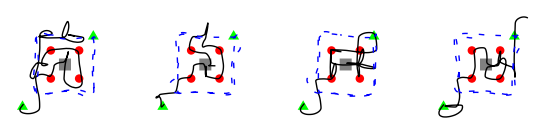

```mathematica
GraphicsGrid[{plots}]
```

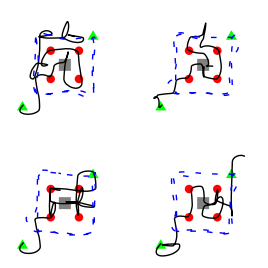

```mathematica
GraphicsGrid[Partition[plots,2]]
```

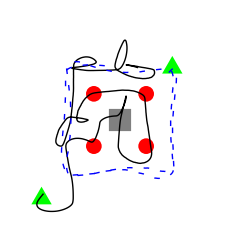

```mathematica
plots[[1]]
```

```mathematica
trajplot[fmt_,fat_,locs_,t_]:=ListLinePlot[{Take[fmt,UpTo[t]],Take[fat,UpTo[t]]},PlotRange->{{-pr,pr},{-pr,pr}},AspectRatio->1,Prolog->locs,GridLines->{gp[Range[0,6]]},Axes->False,PlotStyle->{{Black,Thick},{Blue,Thick,AbsoluteDashing[{4,8}]}}];
```

```mathematica
maxlen=Max[Map[Length,Join[cmt,cat,lmt,lat]]];
frames=Table[GraphicsGrid[{Table[trajplot[lmt[[i]],lat[[i]],llocs,t],{i,1,Length[lmt]}],Table[trajplot[cmt[[i]],cat[[i]],clocs,t],{i,1,Length[cmt]}]}],{t,1,maxlen}];
```

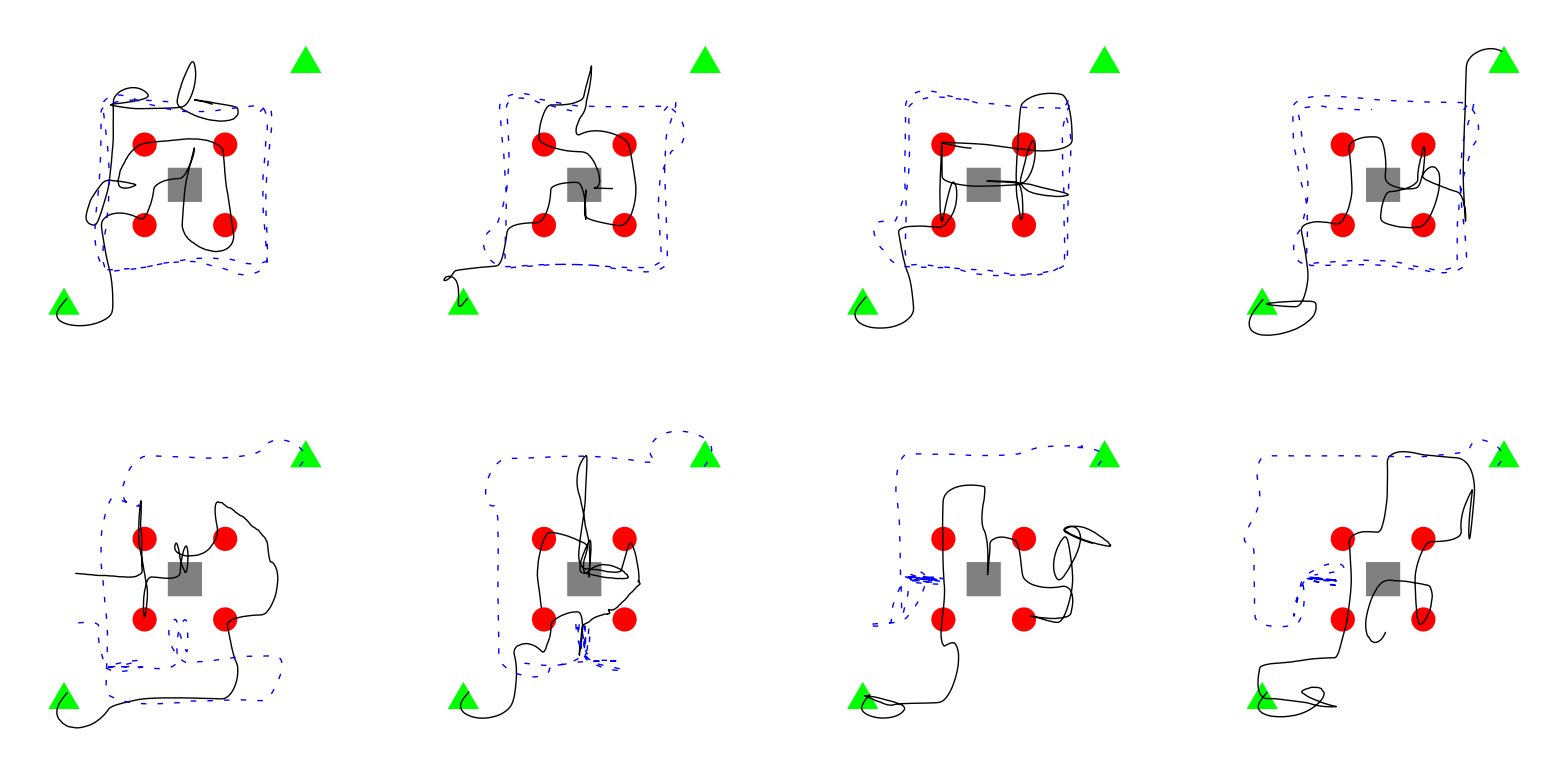

```mathematica
Last[frames]
```

```mathematica
suffix=Table[Last[frames],30];
```

```mathematica
Export["Downloads/combined.avi",Join[frames,suffix],"FrameRate"->30,ImageSize->{1024,512}]
```

Downloads/combined.avi

```mathematica
maxlen
```

1150